#### Run common_funs, ES_FindSymGroups., BC_ChooseTmat, BC_DirectPath

```mathematica
SigCurve=TET;
nm=nm1;
```

```mathematica
Tmat1==TORTH
Tmat2==TTET
```

#### Get data from TrivPathToISO.

```mathematica
dt
```

#### Check the beta for the peak of the discretized curve

```mathematica
betamax =Max[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree&/@Ranget]
```

#### Round is necessary for Mathematica to recognize, for example, that 0.25 + 0.05 = 0.3

```mathematica
slope[t_]:=((βT[TT[Round[t+dt,.05],Tmat1,Tmat2],SigCurve]-βT[TT[t,Tmat1,Tmat2],SigCurve])/Degree)/dt;
```

#### Slope of each segment

```mathematica
MatrixNote[Tmat]
Ranget
dt
TableForm[Join[{{"   t","  βTET","  slope"}},{PaddedForm[#,{2,2}],PaddedForm[Round[βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree,.001],{4,3}],PaddedForm[slope[#],{5,2}]}&/@Ranget]]
```

#### Find the intersection between t = tt1 and t = tt2

```mathematica
tt1=.2;tt2=.4;
beta1=βT[TT[tt1,Tmat1,Tmat2],SigCurve]/Degree;
beta2=βT[TT[tt2,Tmat1,Tmat2],SigCurve]/Degree;
peak=({t,beta}/.Solve[(beta-beta1)/(t-tt1)==slope[tt1]&&(beta-beta2)/(t-tt2)==slope[tt2],{t,beta}])[[1]]
```

```mathematica
MatrixNote[Tmat]
Ranget
dt
plot=Graphics[{PointSize[.015],
Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]],
{ColorData["Rainbow"][0/6],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget},Axes->True,AxesOrigin->{t1,0},AspectRatio->.5,ImageSize->500,Ticks->{Range[0,1,.2],Range[0,8,2]},TicksStyle->14]
```

#### Determine the color scale for the subset of maps to plot

```mathematica
npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tmat1,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]
AlphaMONOvalues=Sort[Table[Alpha[Tmat2,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]
```

```mathematica
cmin=0;cmax=20; dc=2;
contours=Range[cmin,cmax,dc];
MaxForScaling=cmax-dc;
```

```mathematica
eye=20xyztp[{30,65}];
AngRad=.05;
ShiftToEye=.02;
tkns=.01;  (* tkns only affects XISO *)
```

#### Because this is a nm1 sequence, all the balls on the bottom have ORTH symmetry (and it is the SAME ORTH U for all)

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
```

#### pick subset of balls

```mathematica
Ranget
ipick={1,5,9,13,17,21};
Ranget[[ipick]]
```

#### Because this is a subset nm1 path, the U are guaranteed to be identical for the ORTH balls on the bottom

```mathematica
OutputFor[Tmat1,Sig1]
```

```mathematica
TwoFoldBottom=Graphics3D[TwoFoldGraphics[Sig1,UT[Tmat1,Sig1],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]];
```

#### t = 0 ball on bottom

```mathematica
tIs0=Show[{cpMONO[Tmat1,contours,MaxForScaling],TwoFoldBottom},options]
```

```mathematica
tIsPt2onBottom=Show[{cpMONO[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],contours,MaxForScaling],TwoFoldBottom},options]
tIsPt3onBottom=Show[{cpMONO[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],contours,MaxForScaling],TwoFoldBottom},options]
tIsPt4onBottom=Show[{cpMONO[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],contours,MaxForScaling],TwoFoldBottom},options]
tIsPt5onBottom=Show[{cpMONO[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],contours,MaxForScaling],TwoFoldBottom},options]
tIsPt6onBottom=Show[{cpMONO[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],contours,MaxForScaling],TwoFoldBottom},options]
```

#### Demonstrate an issue related to how Mathematica is storing values.

```mathematica
(* MatrixForm[Chop[Closest[TT[#,Tmat1,Tmat2],SigCurve],0.001]]&/@Ranget *)
```

```mathematica
(* MatrixForm[Chop[UT[TT[#,Tmat1,Tmat2],SigCurve],0.001]]&/@Ranget *)
```

```mathematica
Ranget[[7]]
Ranget[[7]]==.3
βT[TT[Ranget[[7]],Tmat1,Tmat2],SigCurve]
βT[TT[.3,Tmat1,Tmat2],SigCurve]
βT[TT[Ranget[[7]],Tmat1,Tmat2],SigCurve]==βT[TT[.3,Tmat1,Tmat2],SigCurve]
```

```mathematica
Ranget[[13]]
Ranget[[13]]==.6
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]
βT[TT[.6,Tmat1,Tmat2],SigCurve]
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]==βT[TT[.6,Tmat1,Tmat2],SigCurve]
```

#### Balls on the top of the triangle

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
```

#### t = 0 ball on top

```mathematica
tIsPt1onTop=Show[{cpMONO[Closest[Tmat1,SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[Tmat1,SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

```mathematica
tIsPt2onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
tIsPt3onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
tIsPt4onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
tIsPt5onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
tIsPt6onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[SigCurve,UT[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

#### t = 1 ball

```mathematica
tIs1=Show[{cpMONO[Tmat2,contours,MaxForScaling],
Graphics3D[TwoFoldGraphics[Sig2,UT[Tmat2,Sig2],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options]
```

#### MAIN PLOT

```mathematica
Ranget[[13]]
βT[TT[0.6,Tmat1,Tmat2],SigCurve]/Degree
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree
```

```mathematica
Drop[ipick,-1]
```

```mathematica
MatrixNote[Tmat]
Ranget
contours
MaxForScaling
PrintEye;
bsize=0.18;
dytop=8;
dybot=-dytop;
dyvertline=3;
dySig=dybot-7;
dxTmat=1.1;
dyTmat=8;
dyU=dyTmat-4;
Graphics[{PointSize[.013],
{PointSize[.001],Point/@{{.1,-14.0},{.5,20.0}}},   (* fake points *)
Line[{{Ranget[[#]],0},{Ranget[[#]],-dyvertline}}]&/@ipick,
Line[{{Ranget[[#]],           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],dyvertline+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@Drop[ipick,-1],
Line[{{0,0},{0,βT[Tmat1,SigCurve]/Degree}}], (* left side line *)
{HueOfΣ[SigCurve],Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]]]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
(* Text[Style["(0, 0)",18],{-.05,0}], *)
(* Text[Style["(1, 0)",18],{1.05,0}], *)
Inset[tIsPt1onTop,{Ranget[[ipick[[1]]]],dytop+βT[Tmat1,SigCurve]/Degree},Center,bsize],
Inset[tIsPt2onTop,{Ranget[[ipick[[2]]]],dytop+βT[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt3onTop,{Ranget[[ipick[[3]]]],dytop+βT[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt4onTop,{Ranget[[ipick[[4]]]],dytop+βT[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt5onTop,{Ranget[[ipick[[5]]]],dytop+βT[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
(*Inset[tIsPt6onTop,{Ranget[[ipick[[6]]]],dytop+βT[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],*)
Inset[tIsPt2onBottom,{Ranget[[ipick[[2]]]],dybot},Center,bsize],
Inset[tIsPt3onBottom,{Ranget[[ipick[[3]]]],dybot},Center,bsize],
Inset[tIsPt4onBottom,{Ranget[[ipick[[4]]]],dybot},Center,bsize],
Inset[tIsPt5onBottom,{Ranget[[ipick[[5]]]],dybot},Center,bsize],
Inset[tIsPt6onBottom,{Ranget[[ipick[[6]]]],dybot},Center,bsize],
Inset[tIs0,{0,dybot},Center,bsize],
Inset[tIs1,{1,dybot},Center,bsize],
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{0,0},{1,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget},
 (* betaΣ for nm2, like Subscript[β, XISO]^ (15.98) *)
Text[Style[SequenceForm[BetaText[SigCurve]," (",Round[βT[Tmat1,SigCurve]/Degree,0.01],")"],16,FontColor->HueOfΣ[SigCurve] ],{-0.5 dt,βT[Tmat1,SigCurve]/Degree},{1,0}],
(* Sigma labels *)
Text[Style[Sig1,16],{0,dySig}],
Text[Style[Sig2,16],{1,dySig}],
 (* Tmat text label *)
Text[Framed[Style[SequenceForm[MatrixNote[Tmat]," [",nm,"]"],16],Background->White,FrameStyle->Black,FrameMargins->Medium ],
{dxTmat,dyTmat},{1,0}],
(* U for nm1 *)
If[nm===nm1,Text[SequenceForm[Style["U",{17,Italic}],Style[" = ",17],Style[MatrixForm[Round[UforNM1,10^-5]],10] ],{dxTmat,dyU},{1,0}]]
},Axes->False,AspectRatio->.5,ImageSize->1000,PlotRange->All]
```

## Brown dt = 0.05, Tmat1=TORTH, Tmat2=TTET, ListSigma = {TET}, nm1 The default is UforNM1 = UXISO, where UXISO = Closest[Tmat,XISO].

#### UforNM1 = UXISO

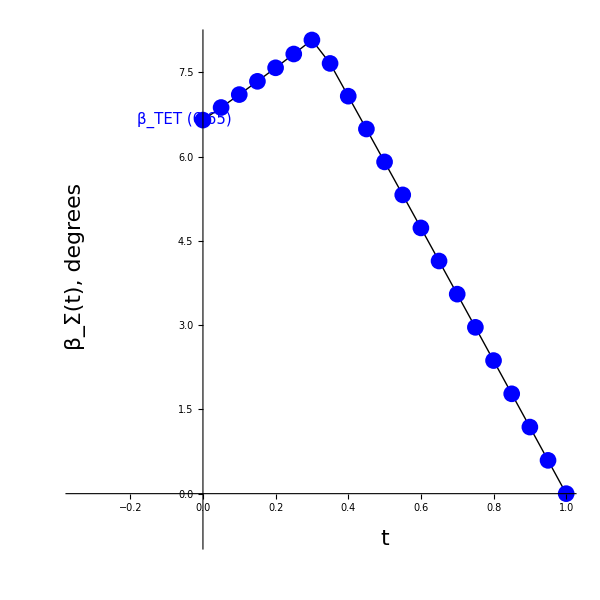

#### UforNM1 = UXISO.ZRot[5Degree]

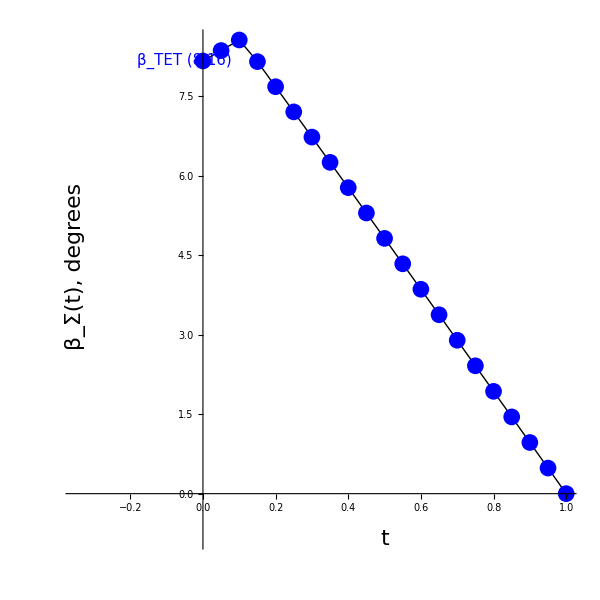

#### UforNM1 = UXISO.ZRot[10Degree]

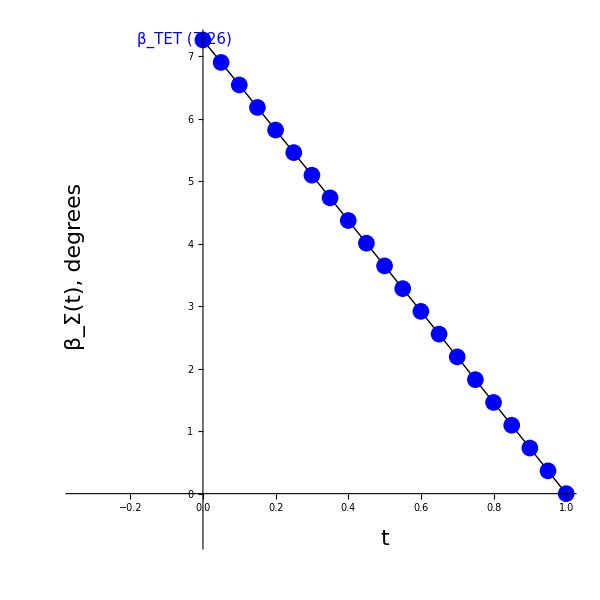

#### UforNM1 = UXISO.ZRot[25Degree]

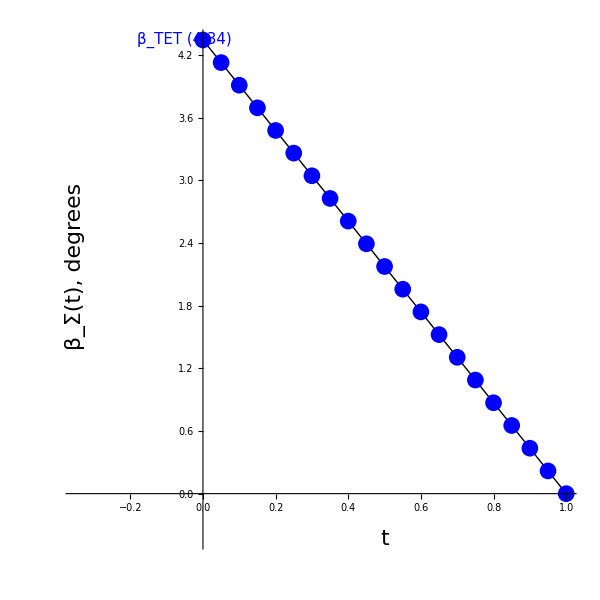

#### UforNM1 = UXISO.ZRot[35Degree]

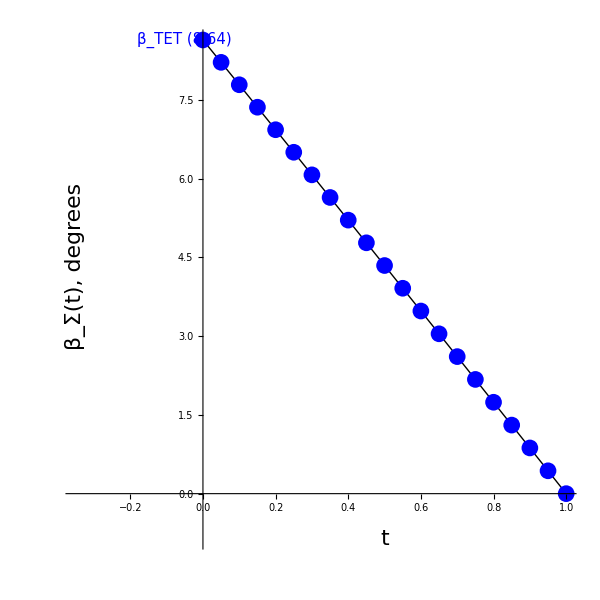

#### UforNM1 = UXISO.ZRot[36Degree]

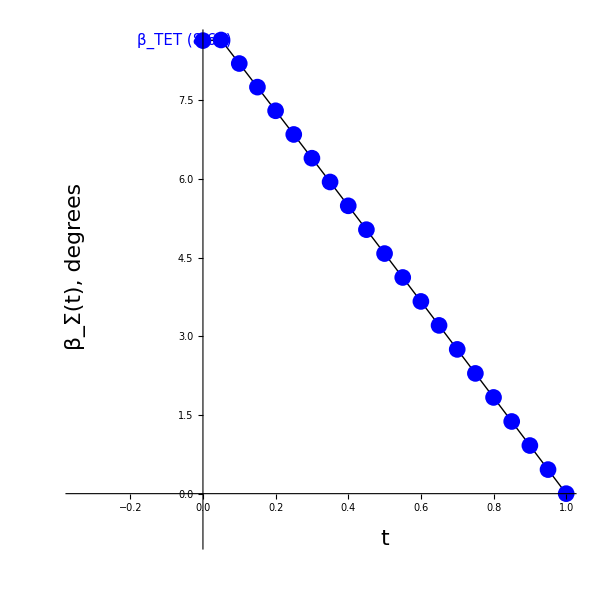

#### UforNM1 = UXISO.ZRot[37Degree]

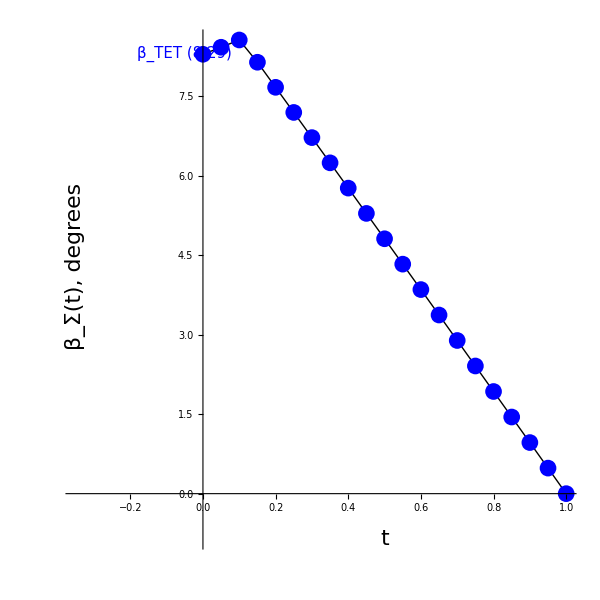

#### UforNM1 = UXISO.ZRot[38Degree]

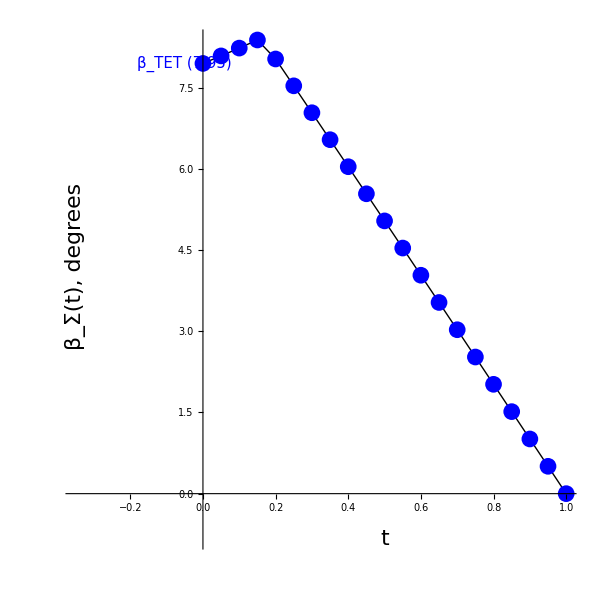

#### UforNM1 = UXISO.ZRot[40Degree]

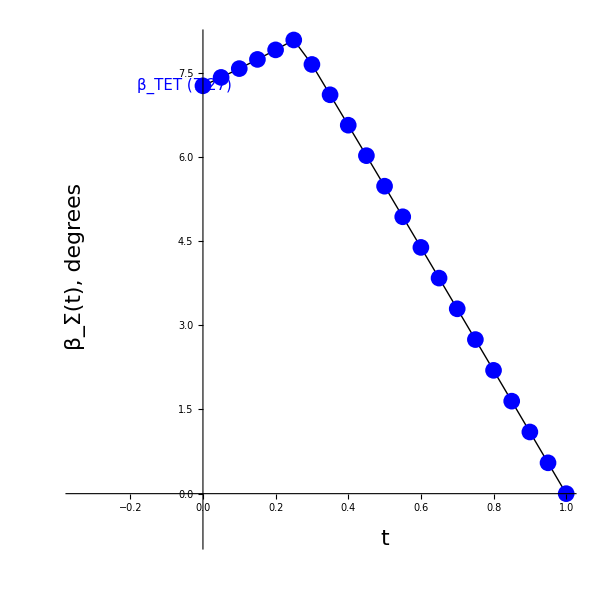

#### UforNM1 = UXISO.ZRot[45Degree]

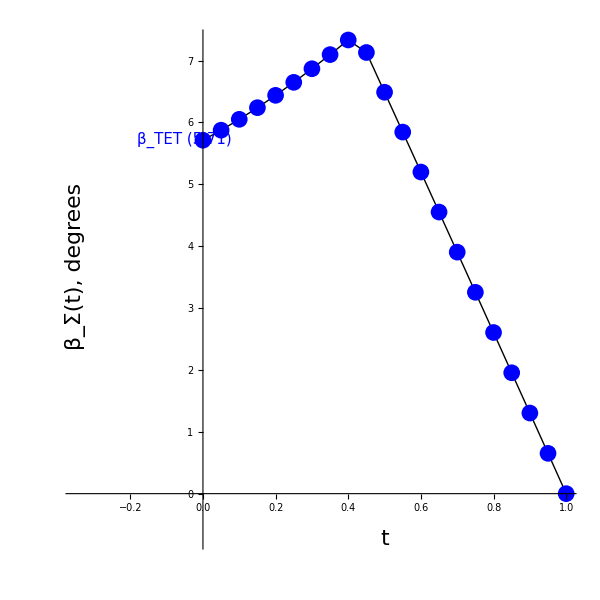

#### UforNM1 = UXISO.ZRot[50Degree]

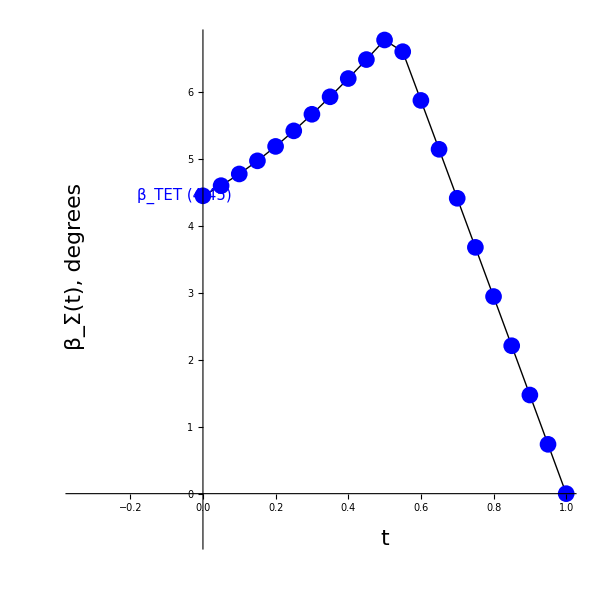

#### UforNM1 = UXISO.ZRot[55Degree]

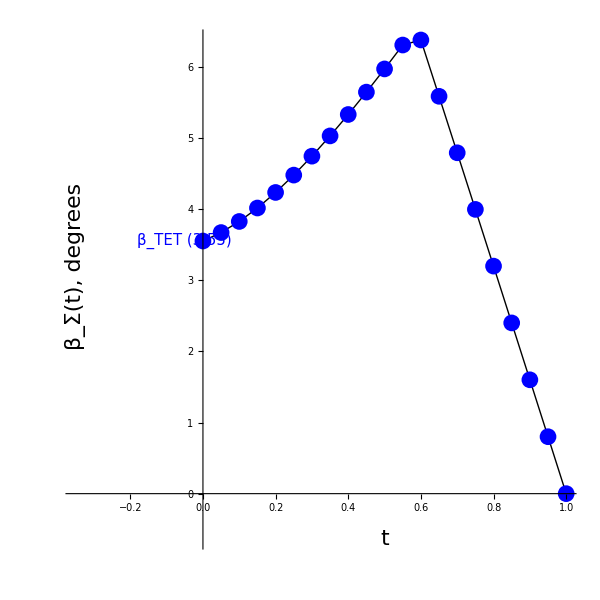

#### UforNM1 = UXISO.ZRot[60Degree]

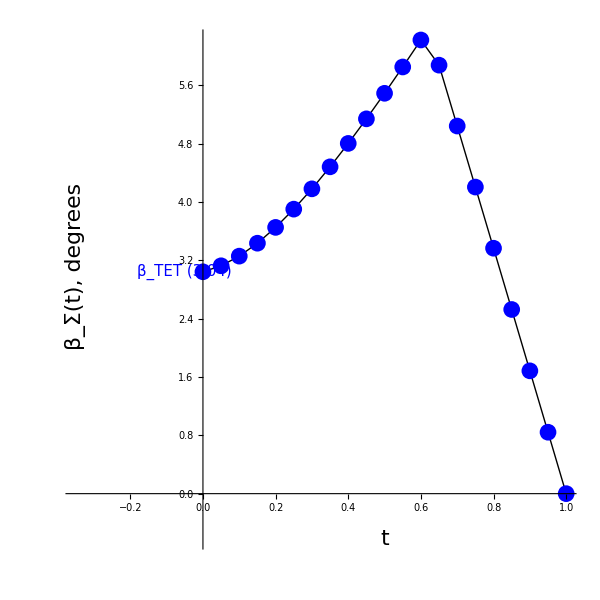

#### UforNM1 = UXISO.ZRot[65Degree]

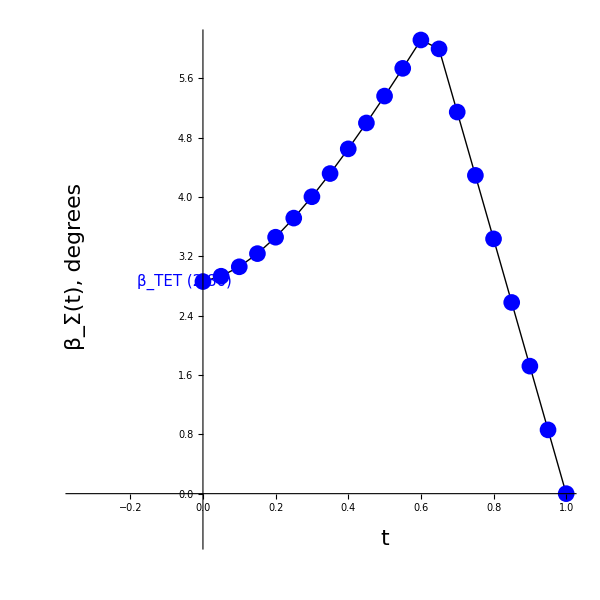

#### UforNM1 = UXISO.ZRot[70Degree]

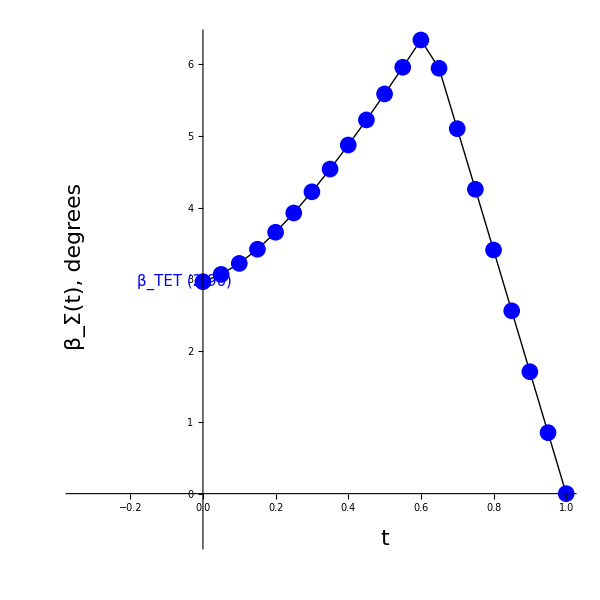

#### UforNM1 = UXISO.ZRot[75Degree]

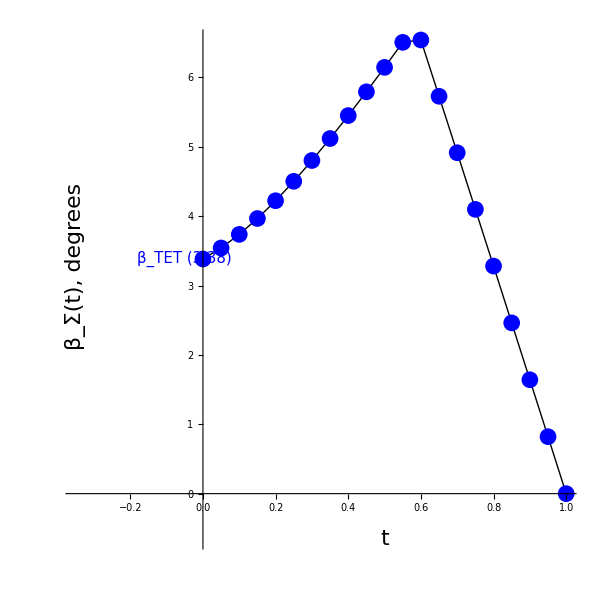

#### UforNM1 = UXISO.ZRot[80Degree]

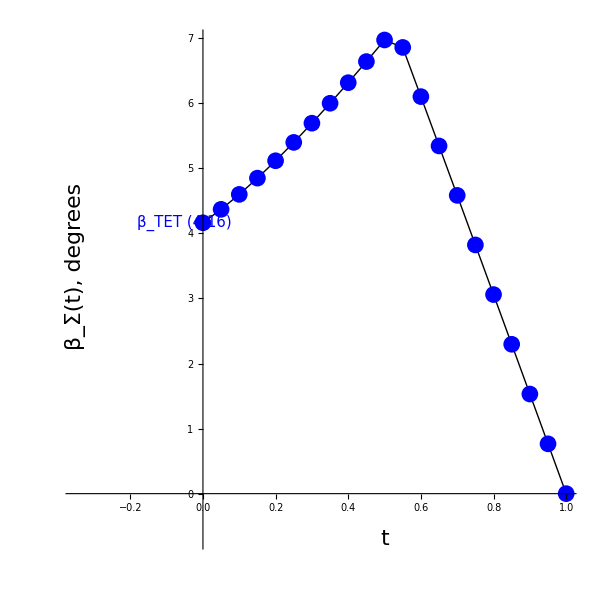

#### UforNM1 = UXISO.ZRot[85Degree]

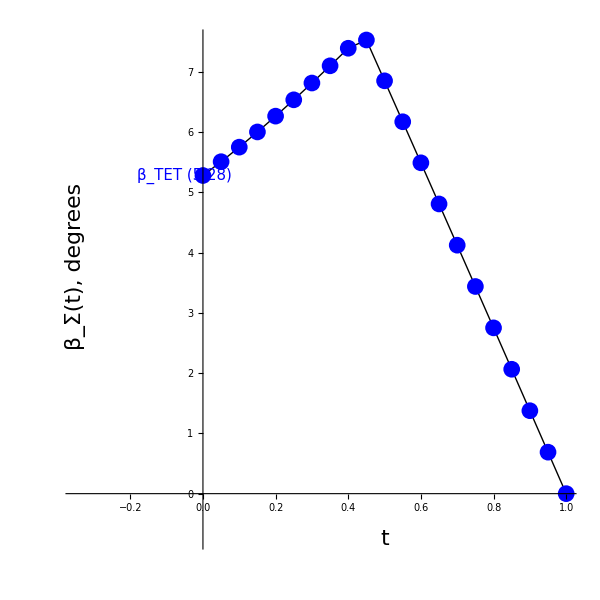

#### UforNM1 = UXISO.ZRot[90Degree]

-Graphics-

#### UforNM1 = UXISO.XRot[1Degree].YRot[1Degree].ZRot[1Degree] (With a small perturbation, the triangle is still present.)